## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.3; qscal=0.345; Q=0.997;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.316753+1.1677×10^-11 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.319254

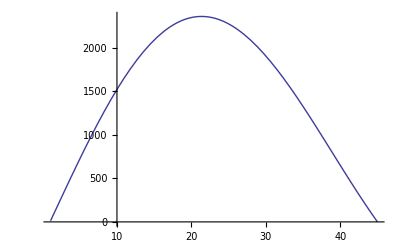

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<176,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,175}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,175}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{45.,1.17106×10^-11},{45.2,1.41513×10^-11},{45.4,1.23076×10^-11},{45.6,1.25656×10^-11},{45.8,1.28011×10^-11},{46.,1.14517×10^-11},{46.2,1.32316×10^-11},{46.4,9.91246×10^-12},{46.6,1.35112×10^-11},{46.8,1.36303×10^-11},{47.,1.37547×10^-11},{47.2,1.38577×10^-11},{47.4,2.93163×10^-11},{47.6,1.3998×10^-11},{47.8,1.38607×10^-11},{48.,1.40519×10^-11},{48.2,1.41174×10^-11},{48.4,1.41339×10^-11},{48.6,1.41407×10^-11},{48.8,1.41383×10^-11},{49.,1.41264×10^-11},{49.2,1.41076×10^-11},{49.4,1.40758×10^-11},{49.6,-1.78596×10^-11},{49.8,1.40109×10^-11},{50.,-2.04335×10^-12},{50.2,1.38917×10^-11},{50.4,1.38304×10^-11},{50.6,1.40345×10^-11},{50.8,1.54651×10^-11},{51.,1.36428×10^-11},{51.2,1.35555×10^-11},{51.4,1.34524×10^-11},{51.6,1.33642×10^-11},{51.8,1.11949×10^-11},{52.,1.32112×10^-11},{52.2,8.96876×10^-13},{52.4,1.29832×10^-11},{52.6,1.28805×10^-11},{52.8,1.27769×10^-11},{53.,1.26716×10^-11},{53.2,1.25722×10^-11},{53.4,1.2457×10^-11},{53.6,1.23641×10^-11},{53.8,1.23449×10^-11},{54.,1.21218×10^-11},{54.2,1.20088×10^-11},{54.4,1.19121×10^-11},{54.6,1.17373×10^-11},{54.8,1.12543×10^-11},{55.,1.15502×10^-11},{55.2,1.16188×10^-11},{55.4,1.13179×10^-11},{55.6,1.1204×10^-11},{55.8,1.10916×10^-11},{56.,1.09702×10^-11},{56.2,1.08523×10^-11},{56.4,1.07291×10^-11},{56.6,9.94928×10^-12},{56.8,1.05206×10^-11},{57.,1.03908×10^-11},{57.2,1.02759×10^-11},{57.4,1.01642×10^-11},{57.6,1.00464×10^-11},{57.8,9.86534×10^-12},{58.,9.82247×10^-12},{58.2,9.70476×10^-12},{58.4,9.42298×10^-12},{58.6,9.53381×10^-12},{58.8,7.03221×10^-12},{59.,2.38709×10^-12},{59.2,3.06849×10^-13},{59.4,8.91299×10^-12},{59.6,8.94836×10^-12},{59.8,-1.73456×10^-12},{60.,2.73406×10^-12},{60.2,8.63504×10^-12},{60.4,8.53228×10^-12},{60.6,8.42966×10^-12},{60.8,8.32839×10^-12},{61.,8.26749×10^-12},{61.2,8.12982×10^-12},{61.4,8.02406×10^-12},{61.6,7.93402×10^-12},{61.8,7.83812×10^-12},{62.,7.75026×10^-12},{62.2,7.64869×10^-12},{62.4,7.2373×10^-12},{62.6,7.46256×10^-12},{62.8,7.32964×10^-12},{63.,7.11487×10^-12},{63.2,7.23716×10^-12},{63.4,7.10262×10^-12},{63.6,7.47939×10^-12},{63.8,6.92958×10^-12},{64.,6.84428×10^-12},{64.2,6.75977×10^-12},{64.4,-7.75756×10^-12},{64.6,6.59339×10^-12},{64.8,6.51273×10^-12},{65.,6.43324×10^-12},{65.2,6.35167×10^-12},{65.4,6.27284×10^-12},{65.6,6.23592×10^-12},{65.8,6.50771×10^-12},{66.,5.68269×10^-12},{66.2,5.96744×10^-12},{66.4,5.89357×10^-12},{66.6,5.8755×10^-12},{66.8,5.74787×10^-12},{67.,5.95711×10^-12},{67.2,5.60569×10^-12},{67.4,5.63471×10^-12},{67.6,5.20833×10^-12},{67.8,5.39949×10^-12},{68.,5.33242×10^-12},{68.2,5.2662×10^-12},{68.4,5.20141×10^-12},{68.6,5.13616×10^-12},{68.8,5.07254×10^-12},{69.,5.00993×10^-12},{69.2,1.90215×10^-11},{69.4,4.88647×10^-12},{69.6,5.36639×10^-12},{69.8,4.75732×10^-12},{70.,4.70719×10^-12},{70.2,4.64793×10^-12},{70.4,4.59366×10^-12},{70.6,4.60162×10^-12},{70.8,4.47954×10^-12},{71.,4.17579×10^-12},{71.2,4.36893×10^-12},{71.4,4.30248×10^-12},{71.6,4.25972×10^-12},{71.8,4.20911×10^-12},{72.,4.1576×10^-12},{72.2,4.09859×10^-12},{72.4,4.05586×10^-12},{72.6,3.99151×10^-12},{72.8,3.95691×10^-12},{73.,3.90847×10^-12},{73.2,3.86028×10^-12},{73.4,3.81361×10^-12},{73.6,3.59222×10^-12},{73.8,3.7209×10^-12},{74.,3.66296×10^-12},{74.2,3.63076×10^-12},{74.4,3.58717×10^-12},{74.6,-1.00528×10^-11},{74.8,-1.84277×10^-11},{75.,3.45801×10^-12},{75.2,3.41565×10^-12},{75.4,3.37409×10^-12},{75.6,3.33329×10^-12},{75.8,5.80344×10^-12},{76.,3.25328×10^-12},{76.2,3.42193×10^-12},{76.4,3.17503×10^-12},{76.6,6.78231×10^-12},{76.8,3.09959×10^-12},{77.,3.06202×10^-12},{77.2,3.02551×10^-12},{77.4,2.87334×10^-12},{77.6,2.95348×10^-12},{77.8,2.93366×10^-12},{78.,2.88334×10^-12},{78.2,2.84955×10^-12},{78.4,3.24027×10^-12},{78.6,2.78264×10^-12},{78.8,2.75059×10^-12},{79.,2.71945×10^-12},{79.2,2.61926×10^-12},{79.4,-1.55159×10^-11},{79.6,2.6195×10^-12},{79.8,2.58964×10^-12},{80.,2.61599×10^-12}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<176,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,175}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,175}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*The imaginary part vs the radius*)
```

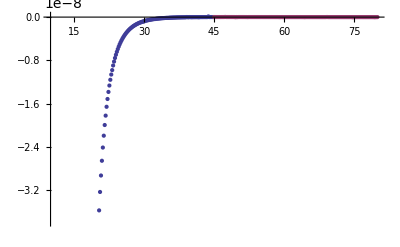

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

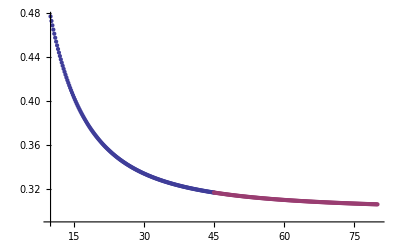

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.15/Q=0.997/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.15/Q=0.997/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.15/Q=0.997/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.15/Q=0.997/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```